Departamento de Matemáticas (Área de Álgebra)

Sesión 6. Grafos III

## Grafos de Euler

#### Definición

Sea G = (W, F) un grafo sin vértices aislados, un camino simple que pase por todos los lados del grafo se dice de que es de Euler. Un camino de Euler cerrado, se dirá que es un ciclo de Euler o circuito de Euler. Un grafo que posea al menos un ciclo de Euler se llamará grafo de Euler.

#### Teorema 7.2 (Caracterización)

SeaG = (W, F) un grafo conexo, entonces:

G es de Euler si y sólo si el grado de cada vértice es par.

#### Ejemplos

Comprobar si un grafo es de Euler es muy sencillo, basta con comprobar la paridad del grado de los vértices y usar el teorema 7.2.

El siguiente grafo es de Euler porque es 4 - regular, todos sus vértices son de grado 4 y par.

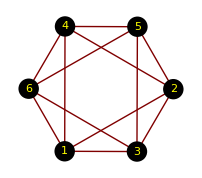

Un ciclo de Euler sería: {1, 2, 4, 1, 3, 5, 6, 3, 2, 5, 4, 6, 1}.

El siguiente grafo no es de Euler porque tiene vértices de grado impar (el 1 el 2).

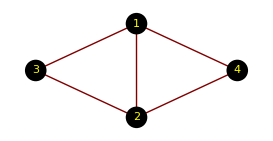

### Mathematica

#### Función 7.18. EULER[]

```mathematica
EULER[matrizadyacencia_]:=Module[{A,i},
   Euler=True;
   If[CONEXO[matrizadyacencia],
      A=matrizadyacencia.matrizadyacencia;
      Do[
         If[Mod[A[[i,i]],2]==1,Euler=False;Break[];];
      ,{i,Length[matrizadyacencia]}];
   ,
      Euler=False;
   ];
   Euler
]
```

#### Programa 7.20. Ciclo de Euler

F=CONJUNTO DE LADOS DE UN GRAFO NO ORIENTADO DE EULER;

tempF=F;
listaciclos={};
While[tempF≠{},
    camino={};
    inicio=tempF[[1,1]];
    otro=tempF[[1,2]];
    AppendTo[camino,tempF[[1,1]]];
    AppendTo[camino,tempF[[1,2]]];
    tempF=Complement[tempF,{tempF[[1]]}];
    While[otro≠inicio,
      j=1;
      ultimo=Last[camino];
      While[tempF[[j,1]]≠ultimo && tempF[[j,2]]≠ultimo ,j++];
      otro=Complement[{tempF[[j]][[1]],tempF[[j]][[2]]},{ultimo}][[1]];
      AppendTo[camino,otro];
      tempF=Complement[tempF,{tempF[[j]]}];
      ];
    AppendTo[listaciclos,camino];
    ];
nuevociclo=listaciclos[[1]];
While[Length[listaciclos]≠1,
    i=2;
    While[Intersection[listaciclos[[1]],listaciclos[[i]]]=={},i++];
    opcion=Intersection[listaciclos[[1]],listaciclos[[i]]][[1]];
    k1=Position[listaciclos[[1]],opcion][[1]][[1]];
    k2=Position[listaciclos[[i]],opcion][[1]][[1]];
    nuevociclo=listaciclos[[1]];
    t=1;
    Do[nuevociclo=Insert[nuevociclo,listaciclos[[i]][[cont]],k1+t];t++;,{cont,k2+1,Length[listaciclos[[i]]]}];
    Do[nuevociclo=Insert[nuevociclo,listaciclos[[i]][[cont]],k1+t];t++;,{cont,2,k2}];
    listaciclos=Delete[listaciclos,i];
    listaciclos=Delete[listaciclos,1];
    AppendTo[listaciclos,nuevociclo];
    ];
nuevociclo

#### Ejemplo 7.17.

```mathematica
A1={{0,1,1,0,0,0,0,0,0,0,0,0},{1,0,0,1,0,0,0,0,0,0,0,0},{1,0,0,0,1,0,0,0,0,0,0,0},{0,1,0,0,0,1,0,0,0,0,0,0},{0,0,1,0,0,1,1,1,0,0,0,0},{0,0,0,1,1,0,1,1,0,0,0,0},{0,0,0,0,1,1,0,1,1,0,0,0},{0,0,0,0,1,1,1,0,0,1,0,0},{0,0,0,0,0,0,1,0,0,0,1,0},{0,0,0,0,0,0,0,1,0,0,0,1},{0,0,0,0,0,0,0,0,1,0,0,1},{0,0,0,0,0,0,0,0,0,1,1,0}};
```

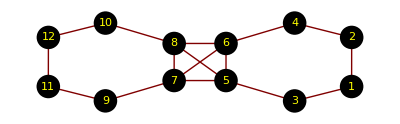

```mathematica
GraphPlot[A1,VertexRenderingFunction->({Black,Disk[#,.2],Yellow,Text[#2,#]}&)]
```

```mathematica
matrizadyacencia=A1;
W=Table[i,{i,Dimensions[matrizadyacencia][[1]]}];
F={};
Do[Do[If[matrizadyacencia[[i,j]]==1,AppendTo[F,i->j]];,{i,j}];
,{j,Dimensions[matrizadyacencia][[1]]}];
```

```mathematica
tempF=F;
listaciclos={};
While[tempF≠{},
camino={};
inicio=tempF[[1,1]];
otro=tempF[[1,2]];
AppendTo[camino,tempF[[1,1]]];
AppendTo[camino,tempF[[1,2]]];
tempF=Complement[tempF,{tempF[[1]]}];
While[otro≠inicio,
j=1;
ultimo=Last[camino];
While[tempF[[j,1]]≠ultimo && tempF[[j,2]]≠ultimo ,j++];
otro=Complement[{tempF[[j]][[1]],tempF[[j]][[2]]},{ultimo}][[1]];
AppendTo[camino,otro];
tempF=Complement[tempF,{tempF[[j]]}];
];
AppendTo[listaciclos,camino];
];
nuevociclo=listaciclos[[1]];
While[Length[listaciclos]≠1,
i=2;
While[Intersection[listaciclos[[1]],listaciclos[[i]]]=={},i++];
opcion=Intersection[listaciclos[[1]],listaciclos[[i]]][[1]];
k1=Position[listaciclos[[1]],opcion][[1]][[1]];
k2=Position[listaciclos[[i]],opcion][[1]][[1]];
nuevociclo=listaciclos[[1]];
t=1;
Do[nuevociclo=Insert[nuevociclo,listaciclos[[i]][[cont]],k1+t];t++;,{cont,k2+1,Length[listaciclos[[i]]]}];
Do[nuevociclo=Insert[nuevociclo,listaciclos[[i]][[cont]],k1+t];t++;,{cont,2,k2}];
listaciclos=Delete[listaciclos,i];
listaciclos=Delete[listaciclos,1];
AppendTo[listaciclos,nuevociclo];
];
nuevociclo
```

{7,6,8,5,3,1,2,4,6,5,7,8,10,12,11,9,7}

```mathematica
<<Combinatorica`
```

```mathematica
EulerianCycle[FromAdjacencyMatrix[A1]]
```

{3,1,2,4,6,5,7,8,10,12,11,9,7,6,8,5,3}

## Grafos de Hamilton

#### Definición

Sea G = (W, F) un grafo (no dirigido) con más de tres vértices , un camino elemental  que pase por todos los vértices del grafo, se dice de que es de Hamilton. Un camino  de Hamilton cerrado, se dirá que es un ciclo de Hamilton o circuito de Hamilton. Un grafo que posea al menos un ciclo de Hamilton se llamará grafo de Hamilton.

*No existe una caracterización.

#### Condiciones suficientes

Sea G = (W, F) un (n, m) - grafo conexo con más de tres vértices tal que gr(v)≥ n/2 para cada vértice v ∈ W, entonces G es un grafo de Hamilton.

Si un grafo posee un vértice que sea articulación, entonces no es de Hamilton.

Sea G = (W, F) un (n, m) - grafo conexo con más de tres vértices tal que gr(v) + gr(w) ≥ n para cada par v y w vértices no adyacentes, entonces G no es de Hamilton.

Sea G = (W, F) un (n, m) - grafo conexo con más de tres vértices tal que m ≥ (n - 1)(n - 2)/2 + 2, entonces G es de Hamilton.

#### Ejemplo: grafo de Hamilton que no es de Euler

K_4 es un ejemplo de Grafo de Hamilton

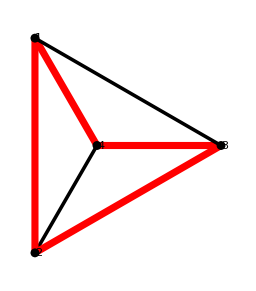

Observemos que el ciclo de Hamilton (en rojo) es el {1, 2, 3, 4, 1}, además nótese que no es de Euler ya que sus vértices son de grado 3, de hecho el grafo es completo y 3 - regular.

K_4 puede verse en el espacio como un tetraedro:

#### Ejemplo: grafo de Euler que no es de Hamilton

Consideremos un grafo que sean dos triángulos con un vértice en común:

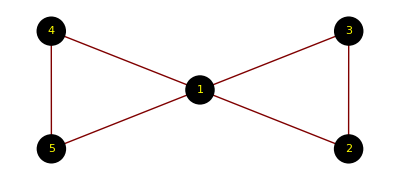

Éste sería un grafo de Euler porque todos sus vértices son de grado par, el ciclo de Euler vendría dado por {1, 2, 3, 1, 4, 5, 1}.

Sin embargo, no es de Hamilton porque tiene una articulación: el vértice 1.

### Mathematica

#### Función 7.21. HAMILTON[]

```mathematica
HAMILTON[A_]:=Module[{ciclos,adyacentes,ultvertice,ciclostemp,k,t,j,i},
ciclos={{1}};
Do[
ciclostemp={};
Do[
adyacentes={};

ultvertice=ciclos[[k]][[i]];
Do[If[A[[ultvertice,j]]==1,AppendTo[adyacentes,j]];,{j,Dimensions[A][[1]]}];

adyacentes=Complement[adyacentes,ciclos[[k]]];
If[adyacentes≠{},

Do[AppendTo[ciclostemp,Append[ciclos[[k]],adyacentes[[t]]]];,{t,Length[adyacentes]}];
];
,{k,Length[ciclos]}];
ciclos=ciclostemp;
,{i,Dimensions[A][[1]]-1}];
ciclostemp={};
Do[If[A[[1,ciclos[[k]][[Dimensions[A][[1]]]]]]==1,AppendTo[ciclostemp,Append[ciclos[[k]],1]];];,{k,Length[ciclos]}];
ciclostemp
];
```

#### Ejemplo 7.19.

```mathematica
HAMILTON[A_]:=Module[{ciclos,adyacentes,ultvertice,ciclostemp,k,t,j,i},
ciclos={{1}};
Do[
ciclostemp={};
Do[
adyacentes={};

ultvertice=ciclos[[k]][[i]];
Do[If[A[[ultvertice,j]]==1,AppendTo[adyacentes,j]];,{j,Dimensions[A][[1]]}];

adyacentes=Complement[adyacentes,ciclos[[k]]];
If[adyacentes≠{},

Do[AppendTo[ciclostemp,Append[ciclos[[k]],adyacentes[[t]]]];,{t,Length[adyacentes]}];
];
,{k,Length[ciclos]}];
ciclos=ciclostemp;
,{i,Dimensions[A][[1]]-1}];
ciclostemp={};
Do[If[A[[1,ciclos[[k]][[Dimensions[A][[1]]]]]]==1,AppendTo[ciclostemp,Append[ciclos[[k]],1]];];,{k,Length[ciclos]}];
ciclostemp
];
```

```mathematica
A1={{0,1,1,0,0,0,0,0,0,0,0,0},{1,0,0,1,0,0,0,0,0,0,0,0},{1,0,0,0,1,0,0,0,0,0,0,0},{0,1,0,0,0,1,0,0,0,0,0,0},{0,0,1,0,0,1,1,1,0,0,0,0},{0,0,0,1,1,0,1,1,0,0,0,0},{0,0,0,0,1,1,0,1,1,0,0,0},{0,0,0,0,1,1,1,0,0,1,0,0},{0,0,0,0,0,0,1,0,0,0,1,0},{0,0,0,0,0,0,0,1,0,0,0,1},{0,0,0,0,0,0,0,0,1,0,0,1},{0,0,0,0,0,0,0,0,0,1,1,0}};
A2={{0,1,1,0,0,1,0,0,0,0,0,0},{1,0,0,1,0,0,0,0,0,0,0,0},{1,0,0,0,1,0,0,0,0,0,0,0},{0,1,0,0,0,1,0,0,0,0,0,0},{0,0,1,0,0,1,1,1,0,0,0,0},{1,0,0,1,1,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,1,1,0,0,1},{0,0,0,0,1,1,1,0,0,1,0,0},{0,0,0,0,0,0,1,0,0,0,1,0},{0,0,0,0,0,0,0,1,0,0,0,1},{0,0,0,0,0,0,0,0,1,0,0,1},{0,0,0,0,0,0,1,0,0,1,1,0}};
A3={{0,1,1,0,0,0,0,0,0,0,0,0},{1,0,0,1,0,0,0,0,0,0,0,0},{1,0,0,1,1,0,0,0,1,0,0,0},{0,1,1,0,0,1,0,0,0,1,0,0},{0,0,1,0,0,1,1,1,0,0,0,0},{0,0,0,1,1,0,1,1,0,0,0,0},{0,0,0,0,1,1,0,1,1,0,0,0},{0,0,0,0,1,1,1,0,0,1,0,0},{0,0,1,0,0,0,1,0,0,1,1,0},{0,0,0,1,0,0,0,1,1,0,0,1},{0,0,0,0,0,0,0,0,1,0,0,1},{0,0,0,0,0,0,0,0,0,1,1,0}};
```

```mathematica
HAMILTON[A1]
```

{{1,2,4,6,7,9,11,12,10,8,5,3,1},{1,2,4,6,8,10,12,11,9,7,5,3,1},{1,3,5,7,9,11,12,10,8,6,4,2,1},{1,3,5,8,10,12,11,9,7,6,4,2,1}}

```mathematica
HAMILTON[A2]
```

{{1,2,4,6,8,10,12,11,9,7,5,3,1},{1,3,5,7,9,11,12,10,8,6,4,2,1}}

```mathematica
HAMILTON[A3]
```

{{1,2,4,6,5,7,8,10,12,11,9,3,1},{1,2,4,6,7,5,8,10,12,11,9,3,1},{1,2,4,6,7,9,11,12,10,8,5,3,1},{1,2,4,6,8,10,12,11,9,7,5,3,1},{1,2,4,10,12,11,9,7,6,8,5,3,1},{1,2,4,10,12,11,9,7,8,6,5,3,1},{1,3,5,6,8,7,9,11,12,10,4,2,1},{1,3,5,7,9,11,12,10,8,6,4,2,1},{1,3,5,8,6,7,9,11,12,10,4,2,1},{1,3,5,8,10,12,11,9,7,6,4,2,1},{1,3,9,11,12,10,8,5,7,6,4,2,1},{1,3,9,11,12,10,8,7,5,6,4,2,1}}

```mathematica
<<Combinatorica`
```

```mathematica
HamiltonianQ[FromAdjacencyMatrix[A1]]
HamiltonianCycle[FromAdjacencyMatrix[A2]]
HamiltonianCycle[FromAdjacencyMatrix[A3],All]
```

True

{1,2,4,6,8,10,12,11,9,7,5,3,1}

{{1,2,4,6,5,7,8,10,12,11,9,3,1},{1,2,4,6,7,5,8,10,12,11,9,3,1},{1,2,4,6,7,9,11,12,10,8,5,3,1},{1,2,4,6,8,10,12,11,9,7,5,3,1},{1,2,4,10,12,11,9,7,6,8,5,3,1},{1,2,4,10,12,11,9,7,8,6,5,3,1},{1,3,5,6,8,7,9,11,12,10,4,2,1},{1,3,5,7,9,11,12,10,8,6,4,2,1},{1,3,5,8,6,7,9,11,12,10,4,2,1},{1,3,5,8,10,12,11,9,7,6,4,2,1},{1,3,9,11,12,10,8,5,7,6,4,2,1},{1,3,9,11,12,10,8,7,5,6,4,2,1}}

## Coloración de un grafo

#### Definiciones

Dado un grafo G = (W, F) (no dirigido), colorear un grafo G consiste en asignar colores a cada vértice de forma que a dos vértices adyacentes no se les asigne un mismo color.

Si el número de colores usado en una coloración de G es n entonces diremos que tenemos una n - coloración de G.

Al menor n para el cual conseguimos una n - coloración se le llama número cromático de G, en tal caso se dice que G es n - cromático.

Una coloración óptima será una n - coloración donde n es el número cromático del grafo.

#### Ejemplo

Consideremos el grafo G con matriz de adyacencia:

A =(0 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 1 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 1 | 1 | 0 | 0
0 | 1 | 0 | 0 | 1 | 0 | 1 | 0
0 | 1 | 1 | 1 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | 1 | 0)

Al contener triángulos, su número cromático es mayor o igual que 3, de hecho es 3 y  una coloración óptima sería:

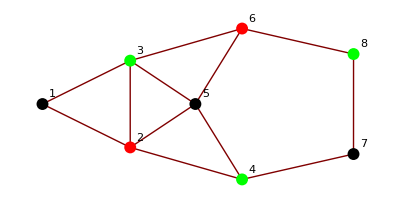

#### Ejemplo (grafos bipartitos)

Los grafos bipartitos son 2 - cromáticos.

Una coloración óptima de K_(3,3) sería:

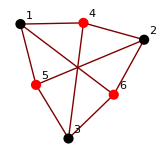

### Mathematica

#### Función 8.1. NCOLORACIONES[]

```mathematica
NCOLORACIONES[matrizadyacencia_,lambda_]:=Module[{coloracionestemp,t,h,i,j,colorady,k},
coloraciones=Table[{k},{k,lambda}];
Do[
coloracionestemp={};
Do[
colorady={};
Do[
If[matrizadyacencia[[t,i]]==1 
,colorady=Union[colorady,{coloraciones[[h]][[t]]}]];
,{t,Length[coloraciones[[h]]]}];
Do[
If[Intersection[{j},colorady]=={},AppendTo[coloracionestemp,Append[coloraciones[[h]],j]]];
,{j,lambda}];
,{h,Length[coloraciones]}];
coloraciones=coloracionestemp;
,{i,2,Dimensions[matrizadyacencia][[1]]}];
coloraciones
];
```

#### Función 8.2. NUMEROCROMATICO[]

```mathematica
NUMEROCROMATICO[matrizadyacencia_]:=Module[{},
t=1;
While[NCOLORACIONES[matrizadyacencia,t]=={},t++];
t]
```

#### Función 8.3. DIBUJAR[]

```mathematica
DIBUJAR[matrizadyacencia_]:=Module[{colores,colorear,COLORES,i},NUMEROCROMATICO[matrizadyacencia];colorear=coloraciones⟦1⟧;colores={"Negro","Rojo","Verde","Azul","Amarillo","Cyan","Marrón","Naranja","Púrpura","Rosa","Gris"};COLORES={Black,Red,Green,Blue,Yellow,Cyan,Brown,Orange,Purple,Pink,Gray};Print["Colores asignados: "];Do[Print["Vértice ",i,", color ",colores⟦colorear⟦i⟧⟧],{i,Length[colorear]}];GraphPlot[matrizadyacencia,VertexRenderingFunction->({COLORES⟦colorear⟦#2⟧⟧,Disk[#1,0.06],Black,Text[#2,{#1[[1]]+.1,#1[[2]]+.1}]}&)]
]
```

#### Ejemplo 8.1.

```mathematica
NCOLORACIONES[matrizadyacencia_,lambda_]:=Module[{coloracionestemp,t,h,i,j,colorady,k},
coloraciones=Table[{k},{k,lambda}];
Do[
coloracionestemp={};
Do[
colorady={};
Do[
If[matrizadyacencia[[t,i]]==1 
,colorady=Union[colorady,{coloraciones[[h]][[t]]}]];
,{t,Length[coloraciones[[h]]]}];
Do[
If[Intersection[{j},colorady]=={},AppendTo[coloracionestemp,Append[coloraciones[[h]],j]]];
,{j,lambda}];
,{h,Length[coloraciones]}];
coloraciones=coloracionestemp;
,{i,2,Dimensions[matrizadyacencia][[1]]}];
coloraciones
];
```

```mathematica
NUMEROCROMATICO[matrizadyacencia_]:=Module[{},
t=1;
While[NCOLORACIONES[matrizadyacencia,t]=={},t++];
t]
```

```mathematica
matrizadyacencia={{0,1,1,0,0,0,0,0},{1,0,1,1,1,0,0,0},{1,1,0,0,1,1,0,0},{0,1,0,0,1,0,1,0},{0,1,1,1,0,1,0,0},{0,0,1,0,1,0,0,1},{0,0,0,1,0,0,0,1},{0,0,0,0,0,1,1,0}};
```

```mathematica
n=8;
K=Table[If[i==j,0,1],{i,n},{j,n}];
```

```mathematica
NUMEROCROMATICO[matrizadyacencia]
```

3

```mathematica
DIBUJAR[matrizadyacencia_]:=Module[{colores,colorear,COLORES,i},NUMEROCROMATICO[matrizadyacencia];colorear=coloraciones⟦1⟧;colores={"Negro","Rojo","Verde","Azul","Amarillo","Cyan","Marrón","Naranja","Púrpura","Rosa","Gris"};COLORES={Black,Red,Green,Blue,Yellow,Cyan,Brown,Orange,Purple,Pink,Gray};Print["Colores asignados: "];Do[Print["Vértice ",i,", color ",colores⟦colorear⟦i⟧⟧],{i,Length[colorear]}];GraphPlot[matrizadyacencia,VertexRenderingFunction->({COLORES⟦colorear⟦#2⟧⟧,Disk[#1,0.06],Black,Text[#2,{#1[[1]]+.1,#1[[2]]+.1}]}&)]
]
```

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Verde

Vértice 4, color Verde

Vértice 5, color Negro

Vértice 6, color Rojo

Vértice 7, color Negro

Vértice 8, color Verde

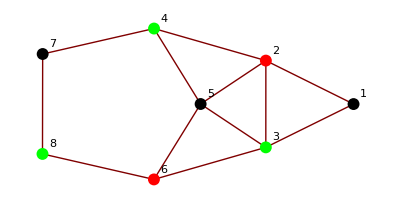

```mathematica
DIBUJAR[matrizadyacencia]
```

```mathematica
<<Combinatorica`
```

```mathematica
ChromaticNumber[FromAdjacencyMatrix[matrizadyacencia]]
```

3

```mathematica
MinimumVertexColoring[FromAdjacencyMatrix[matrizadyacencia]]
```

{1,2,3,3,1,2,1,3}

## Grafos Planos

#### Definición

Un grafo se dirá plano si podemos representarlo gráficamente en el plano de forma que no se corten sus lados.

#### Grafos homeomorfos

Sea G = (W, F) un grafo no orientado y sea e = {w_1, w_2} un lado, una subdivisión elemental de G, es otro grafo G_1 = (W_1, F_1) donde W_1 = W ∪ {w} y F_1 = (F - {e}) ∪ {{w_1, w}, {w, w_2}} para algún w ∉ W.

Dos grafos G_1 y G_2 diremos que son homeomorfos si existen dos grafos isomorfos H_1 y H_2 tales que de H_1 llegamos a G_1 y de H_2 a G_2 por sucesivas subdivisiones o bien son isomorfos.

#### Teorema 8.2 (de Kuratowski) (Caracterización)

Un grafo es plano si y sólo si no contiene un subgrafo homeomorfo a K_5 o K_(3,3).

#### Ejemplo

Encontrar representaciones planas de un grafo no siempre es evidente. Por ejemplo, el siguiente grafo es plano:

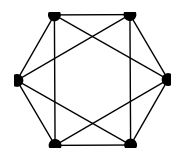

Y una representación plana sería.

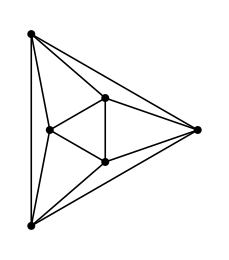

#### Ejemplo (Grafo de Petersen)

Encontrar en un grafo no plano, un subgrafo homeomorfo a K_5 o K_(3,3)

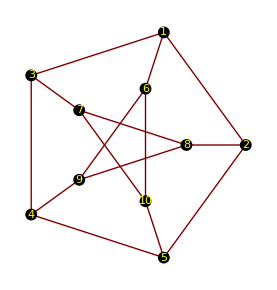

En la siguiente ilustración vemos un subgrafo que es K_(3,3)

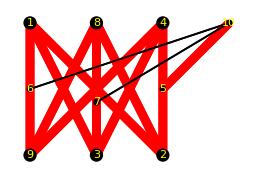

### Mathematica

#### Función 8.11. D3[]

```mathematica
D3[matrizadyacencia_,i_,j_]:=Table[If[(k1==i && k2==j)||(k1==j &&k2==i),1,matrizadyacencia[[k1,k2]]],{k1,Dimensions[matrizadyacencia][[1]]},{k2,Dimensions[matrizadyacencia][[2]]}]
```

#### Función 8.12. QUITARVERTICESGRADO210[]

```mathematica
QUITARVERTICESGRADO210[matrizadyacencia_]:=Module[{grado2,t,W1,A,i,k,m,adya,k1,k2,k3,k4,adyacentes,j},

Nueva=matrizadyacencia;
A=Nueva.Nueva;
grado2=True;t=1;
While[grado2,
W1={};

grado2=False;
If[Dimensions[A][[1]]>2,
Do[If[A[[i,i]]==2 || A[[i,i]]==1 || A[[i,i]]==0, AppendTo[W1,i];grado2=True;],{i,Dimensions[A][[1]]}];
If[grado2,

Sort[W1];
Do[
m=W1[[Length[W1]-k+1]];

If[Dimensions[Nueva][[1]]>2,

If[A[[m,m]]==2,
adyacentes={};
Do[If[Nueva[[m,adya]]==1,AppendTo[adyacentes,adya]],{adya,Dimensions[Nueva][[1]]}];
Nueva=D3[Nueva,adyacentes[[1]],adyacentes[[2]]]
];
Nueva=Table[
If[k1≥m,k3=k1+1,k3=k1];
If[k2≥m,k4=k2+1,k4=k2];
Nueva[[k3,k4]]
,{k1,Dimensions[Nueva][[1]]-1},{k2,Dimensions[Nueva][[2]]-1}];


A=Nueva.Nueva;
];

,{k,Length[W1]}];
];

];t++;];
Nueva]
```

#### Función 8.13. K33[]

```mathematica
<<"Combinatorica`";
```

```mathematica
K33[W_,matrizadyacencia_]:=Module[{subconjuntos,nok33,i,k1,k2},
contiene=False;
subconjuntos=KSubsets[Complement[W,{W[[1]]}],2];
Do[
nok33=False;
A=Join[subconjuntos[[i]],{W[[1]]}];
B=Complement[W,A];
Do[
If[Sum[matrizadyacencia[[A[[k1]],B[[k2]]]],{k2,3}]<3,nok33=True;Break[];];
,{k1,3}];
If[!nok33,contiene=True;Break[];];
,{i,Length[subconjuntos]}];
contiene
]
```

#### Función 8.14. HOMEOMORFOK5K33[]

```mathematica
HOMEOMORFOK5K33[matrizadyacencia_]:=Module[{Subconjuntos,i,j,cont1,matrizadyacenciaK5,Nueva},
Nueva=QUITARVERTICESGRADO210[matrizadyacencia];
homeo=True;
If[Dimensions[Nueva][[1]]==6,
If[K33[{1,2,3,4,5,6},Nueva],homeo=False;]];
matrizadyacenciaK5=Table[If[i==j,0,1],{i,5},{j,5}];
If[Dimensions[Nueva][[1]]==5,If[Nueva==matrizadyacenciaK5,homeo=False;]];
homeo
]
```

#### Función 8.15. PLANO[]

```mathematica
PLANO[matrizadyacencia_]:=Module[{Nueva,k2,k3,subclados,lados},
Nueva=QUITARVERTICESGRADO210[matrizadyacencia];
tiempo=TimeUsed[];
plano=True;

vertices=Table[i,{i,Dimensions[Nueva][[1]]}];
lados={};

Do[
Do[
If[Nueva[[t1,t2]]==1,AppendTo[lados,t1->t2]];
,{t1,t2}];
,{t2,Dimensions[Nueva][[1]]}];

Do[
subclados=KSubsets[lados,k2];
Do[
If[HOMEOMORFOK5K33[MATRIZADYACENCIA[vertices,subclados[[k3]]]]==False,plano=False;subgrafo=subclados[[k3]];Break[]];
If[TimeUsed[]-tiempo>5,Print[k2-9," ",Length[subclados]-k3];tiempo=TimeUsed[];];
,{k3,Length[subclados]}];
If[!plano,Break[]];
,{k2,Length[lados],9,-1}];


plano
]
```

#### Ejemplo 8.18.

```mathematica
D3[matrizadyacencia_,i_,j_]:=Table[If[(k1==i && k2==j)||(k1==j &&k2==i),1,matrizadyacencia[[k1,k2]]],{k1,Dimensions[matrizadyacencia][[1]]},{k2,Dimensions[matrizadyacencia][[2]]}]
```

```mathematica
QUITARVERTICESGRADO210[matrizadyacencia_]:=Module[{grado2,t,W1,A,i,k,m,adya,k1,k2,k3,k4,adyacentes,j},

Nueva=matrizadyacencia;
A=Nueva.Nueva;
grado2=True;t=1;
While[grado2,
W1={};

grado2=False;
If[Dimensions[A][[1]]>2,
Do[If[A[[i,i]]==2 || A[[i,i]]==1 || A[[i,i]]==0, AppendTo[W1,i];grado2=True;],{i,Dimensions[A][[1]]}];
If[grado2,

Sort[W1];
Do[
m=W1[[Length[W1]-k+1]];

If[Dimensions[Nueva][[1]]>2,

If[A[[m,m]]==2,
adyacentes={};
Do[If[Nueva[[m,adya]]==1,AppendTo[adyacentes,adya]],{adya,Dimensions[Nueva][[1]]}];
Nueva=D3[Nueva,adyacentes[[1]],adyacentes[[2]]]
];
Nueva=Table[
If[k1≥m,k3=k1+1,k3=k1];
If[k2≥m,k4=k2+1,k4=k2];
Nueva[[k3,k4]]
,{k1,Dimensions[Nueva][[1]]-1},{k2,Dimensions[Nueva][[2]]-1}];


A=Nueva.Nueva;
];

,{k,Length[W1]}];
];

];t++;];
Nueva]
```

```mathematica
<<Combinatorica`;
```

```mathematica
K33[W_,matrizadyacencia_]:=Module[{subconjuntos,nok33,i,k1,k2},
contiene=False;
subconjuntos=KSubsets[Complement[W,{W[[1]]}],2];
Do[
nok33=False;
A=Join[subconjuntos[[i]],{W[[1]]}];
B=Complement[W,A];
Do[
If[Sum[matrizadyacencia[[A[[k1]],B[[k2]]]],{k2,3}]<3,nok33=True;Break[];];
,{k1,3}];
If[!nok33,contiene=True;Break[];];
,{i,Length[subconjuntos]}];
contiene
]
```

```mathematica
HOMEOMORFOK5K33[matrizadyacencia_]:=Module[{Subconjuntos,i,j,cont1,matrizadyacenciaK5,Nueva},
Nueva=QUITARVERTICESGRADO210[matrizadyacencia];
homeo=True;
If[Dimensions[Nueva][[1]]==6,
If[K33[{1,2,3,4,5,6},Nueva],homeo=False;]];
matrizadyacenciaK5=Table[If[i==j,0,1],{i,5},{j,5}];
If[Dimensions[Nueva][[1]]==5,If[Nueva==matrizadyacenciaK5,homeo=False;]];
homeo
]
```

```mathematica
MATRIZADYACENCIA[W_,F_]:=Module[{i,k},
matrizadyacencia=Table[0,{i,Length[W]},{j,Length[W]}];
Do[matrizadyacencia[[F[[k,1]],F[[k,2]]]]=1;
matrizadyacencia[[F[[k,2]],F[[k,1]]]]=1;
,{k,Length[F]}];
matrizadyacencia];
```

```mathematica
HOMEOMORFOK5K33v2[matrizadyacencia_]:=Module[{Subconjuntos,i,j,cont1,matrizadyacenciaK5,Nueva,lados},
Nueva=QUITARVERTICESGRADO210[matrizadyacencia];
homeo=True;
lados=0;
Do[
Do[
If[Nueva[[t1,t2]]==1,lados++];
,{t1,t2}];
,{t2,Dimensions[Nueva][[1]]}];

If[Dimensions[Nueva][[1]]==6 &&lados==9,
If[K33[{1,2,3,4,5,6},Nueva],homeo=False;]];

If[Dimensions[Nueva][[1]]==5 &&lados ==10,homeo=False;];
homeo
]
```

```mathematica
PLANO[matrizadyacencia_]:=Module[{Nueva,k2,k3,subclados,lados},
Nueva=QUITARVERTICESGRADO210[matrizadyacencia];
tiempo=TimeUsed[];
plano=True;

vertices=Table[i,{i,Dimensions[Nueva][[1]]}];
lados={};

Do[
Do[
If[Nueva[[t1,t2]]==1,AppendTo[lados,t1->t2]];
,{t1,t2}];
,{t2,Dimensions[Nueva][[1]]}];

Do[
subclados=KSubsets[lados,k2];
Do[
If[HOMEOMORFOK5K33[MATRIZADYACENCIA[vertices,subclados[[k3]]]]==False,plano=False;subgrafo=subclados[[k3]];Break[]];
If[TimeUsed[]-tiempo>5,Print[k2-9," ",Length[subclados]-k3];tiempo=TimeUsed[];];
,{k3,Length[subclados]}];
If[!plano,Break[]];
,{k2,Length[lados],9,-1}];


plano
]
```

```mathematica
matrizadyacencia={{0,1,1,1,0,0,0,1},{1,0,1,1,0,0,0,1},{1,1,0,1,0,0,0,1},{1,1,1,0,1,1,0,0},{0,0,0,1,0,1,0,0},{0,0,0,1,1,0,1,1},{0,0,0,0,0,1,0,1},{1,1,1,0,0,1,1,0}};
```

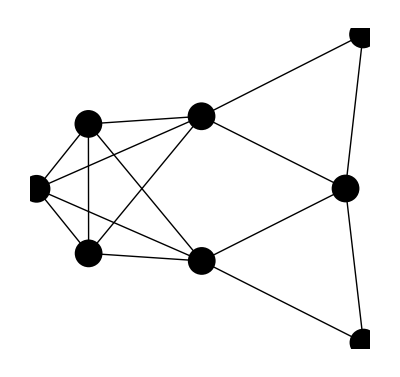

```mathematica
GraphPlot[matrizadyacencia,PlotStyle->{Black,PointSize[.05]}]
```

```mathematica
PLANO[matrizadyacencia]
```

False

```mathematica
subgrafo
```

{1→2,1→3,2→3,1→4,2→4,3→4,1→5,2→5,3→5,4→5}

## Árboles y bosques

#### Definiciones

Un árbol es un grafo conexo y sin ciclos elementales (circuitos).

Un bosque es un grafo sin ciclos elementales, esto es, es un grafo donde cada componente conexa es un árbol.

#### Teorema 8.4 (Caracterización)

Sea G un (p, q) - grafo conexo, entonces:

G es un árbol ⇔ p = q + 1.

#### Ejemplos

Ejemplos de árboles

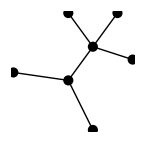

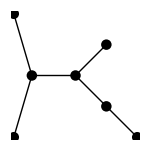

Ejemplos de bosques

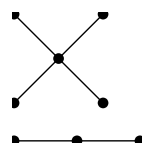

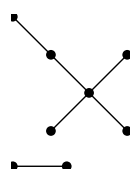

### Mathematica

#### Función 8.19. CICLOSELEMENTALES[]

```mathematica
CICLOSELEMENTALES[vertice1_,longitud_,A_]:=Module[{i,ultvertice,caminos,adyacentes,caminostemp,k,j,t},
caminos={{vertice1}};
Do[
caminostemp={};
Do[
adyacentes={};

ultvertice=caminos[[k]][[i]];
Do[If[A[[ultvertice,j]]==1,AppendTo[adyacentes,j]];,{j,Dimensions[A][[1]]}];

adyacentes=Complement[adyacentes,caminos[[k]]];
If[adyacentes≠{},

Do[AppendTo[caminostemp,Append[caminos[[k]],adyacentes[[t]]]];,{t,Length[adyacentes]}];
];
,{k,Length[caminos]}];
caminos=caminostemp;
,{i,longitud-1}];
caminostemp={};
Do[If[A[[caminos[[k]][[longitud]],vertice1]]==1,AppendTo[caminostemp,Append[caminos[[k]],vertice1]];];,{k,Length[caminos]}];
caminostemp
];
```

#### Función 8.20. BOSQUE[]

```mathematica
BOSQUE[matrizadyacencia_]:=Module[{n,longitud,i,},
bosque=True;
n=Dimensions[matrizadyacencia][[1]];
Do[
potencia=MatrixPower[matrizadyacencia,longitud];
Do[
If[potencia[[i,i]]>0, 
If[CICLOSELEMENTALES[i,longitud,matrizadyacencia]≠{},bosque=False;Break[];];
];
,{i,n}];
If[bosque==False,Break[];];
,{longitud,3,n}];
bosque
];
```

#### Función 8.21. ARBOL[]

```mathematica
CONEXO[A_]:=Module[{i,j,B},
B=Sum[MatrixPower[A,j],{j,Dimensions[A][[1]]}];
conexo=True;
Do[
Do[If[i≠j && B[[i,j]]==0,conexo=False;];
,{i,Dimensions[B][[1]]}];
,{j,Dimensions[B][[1]]}];
conexo
]
```

```mathematica
ARBOL[matrizadyacencia_]:=Module[{i,j,lados},
arbol=False;
If[CONEXO[matrizadyacencia],
arbol=(Dimensions[matrizadyacencia][[1]]==(Sum[matrizadyacencia[[i,j]],{i,Dimensions[matrizadyacencia][[1]]},{j,Dimensions[matrizadyacencia][[2]]}]/2)+1);
];
arbol
]
```

#### Función 8.22. BOSQUE2[]

```mathematica
COMPONENTESCONEXAS[matrizadyacencia_]:=Module[{j,B,conjunto,temp},
B=Sum[MatrixPower[matrizadyacencia,j],{j,Dimensions[matrizadyacencia][[1]]}];
componentesconexas={};
conjunto=Table[i,{i,Dimensions[B][[1]]}];
While[conjunto≠{},
temp={conjunto[[1]]};
Do[
If[B[[conjunto[[1]],conjunto[[i]]]]≠0,AppendTo[temp,conjunto[[i]]];];
,{i,2,Length[conjunto]}];
AppendTo[componentesconexas,temp];
conjunto=Complement[conjunto,temp];
];
componentesconexas
]
```

```mathematica
IND2[W1_,matrizadyacencia_]:=Module[{n,i,j},
n=Length[W1];
matrizadyacencia2=Table[0,{i,n},{j,n}];
Do[Do[
matrizadyacencia2[[i,j]]=matrizadyacencia[[W1[[i]],W1[[j]]]];
,{i,n}];
,{j,n}];
matrizadyacencia2
];
```

```mathematica
BOSQUE2[matrizadyacencia_]:=Module[{componentes,i},
bosque=True;
componentes=COMPONENTESCONEXAS[matrizadyacencia];
Do[
If[ARBOL[IND2[componentes[[i]],matrizadyacencia]]==False,bosque=False];
,{i,Length[componentes]}];
bosque]
```

#### Ejemplo 8.27.

```mathematica
n=4;
t=1;t1=1;F={};
Do[Do[Do[
t++;
AppendTo[F,t1->t];
,{k,i}];
t1++;
,{j,(i-1)!}];,{i,1,n}];
F
```

{1→2,2→3,2→4,3→5,3→6,3→7,4→8,4→9,4→10,5→11,5→12,5→13,5→14,6→15,6→16,6→17,6→18,7→19,7→20,7→21,7→22,8→23,8→24,8→25,8→26,9→27,9→28,9→29,9→30,10→31,10→32,10→33,10→34}

```mathematica
MATRIZADYACENCIA[W_,F_]:=Module[{},
matrizadyacencia=Table[0,{i,Length[W]},{j,Length[W]}];
Do[matrizadyacencia[[F[[k,1]],F[[k,2]]]]=1;
matrizadyacencia[[F[[k,2]],F[[k,1]]]]=1;
,{k,Length[F]}];
matrizadyacencia];
```

```mathematica
matriz=MATRIZADYACENCIA[Table[i,{i,34}],F];
```

```mathematica
CONEXO[A_]:=Module[{i,j,B},
B=Sum[MatrixPower[A,j],{j,Dimensions[A][[1]]}];
conexo=True;
Do[
Do[If[i≠j && B[[i,j]]==0,conexo=False;];
,{i,Dimensions[B][[1]]}];
,{j,Dimensions[B][[1]]}];
conexo
]
```

```mathematica
CICLOSELEMENTALES[vertice1_,longitud_,A_]:=Module[{i,ultvertice,caminos,adyacentes,caminostemp,k,j,t},
caminos={{vertice1}};
Do[
caminostemp={};
Do[
adyacentes={};

ultvertice=caminos[[k]][[i]];
Do[If[A[[ultvertice,j]]==1,AppendTo[adyacentes,j]];,{j,Dimensions[A][[1]]}];

adyacentes=Complement[adyacentes,caminos[[k]]];
If[adyacentes≠{},

Do[AppendTo[caminostemp,Append[caminos[[k]],adyacentes[[t]]]];,{t,Length[adyacentes]}];
];
,{k,Length[caminos]}];
caminos=caminostemp;
,{i,longitud-1}];
caminostemp={};
Do[If[A[[caminos[[k]][[longitud]],vertice1]]==1,AppendTo[caminostemp,Append[caminos[[k]],vertice1]];];,{k,Length[caminos]}];
caminostemp
];
```

```mathematica
BOSQUE[matrizadyacencia_]:=Module[{n,longitud,i,},
bosque=True;
n=Dimensions[matrizadyacencia][[1]];
Do[
potencia=MatrixPower[matrizadyacencia,longitud];
Do[
If[potencia[[i,i]]>0, 
If[CICLOSELEMENTALES[i,longitud,matrizadyacencia]≠{},bosque=False;Break[];];
];
,{i,n}];
If[bosque==False,Break[];];
,{longitud,3,n}];
bosque
];
```

```mathematica
CONEXO[matriz] && BOSQUE[matriz]
```

True

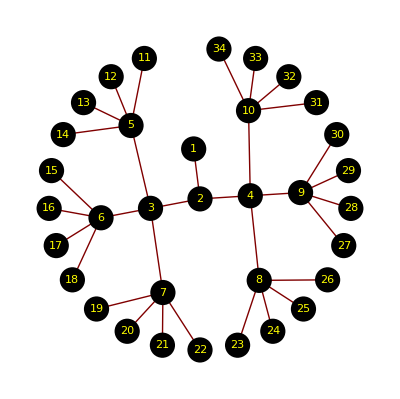

```mathematica
GraphPlot[F,VertexRenderingFunction->({Black,Disk[#,.2],Yellow,Text[#2,#]}&)]
```

```mathematica
<<GraphUtilities`
```

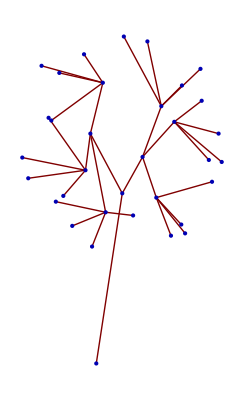

```mathematica
GRAFO=F;
vert=34;
coordenadas=Table[{GraphCoordinates[GRAFO]⟦i⟧⟦1⟧+RandomReal[{0,1}],GraphCoordinates[GRAFO]⟦i⟧⟦2⟧+RandomReal[{0,1}]},{i,vert}];
coordenadas⟦1,1⟧=2;
coordenadas⟦1,2⟧=-2;
Do[coordenadas⟦i,2⟧++;,{i,3,vert}]
GraphPlot[GRAFO,VertexCoordinateRules->coordenadas]
```

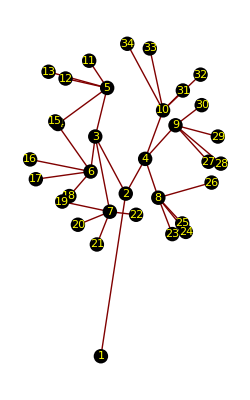

```mathematica
GraphPlot[GRAFO,VertexRenderingFunction->({Black,Disk[#,.2],Yellow,Text[#2,#]}&),VertexCoordinateRules->coordenadas]
```